First function:

```mathematica
func1[x_,y_,z_]=x^3*y^5*Exp[-z]*(3+Cos[x+y+z])
```

ⅇ^-z x^3 y^5 (3+Cos[x+y+z])

```mathematica
xfunc1[x_]=x^3
xnorm1=Integrate[xfunc1[x],{x,0,2}]
xpdf1[x_]=xfunc1[x]/xnorm1
xcdf1[x_]=Integrate[xpdf1[xt],{xt,0,x}]
xicdf1[alpha_]=x/.Solve[xcdf1[x]==alpha,x][[4]]
xrand1[]:=xicdf1[RandomReal[]]
```

x^3

4

x^3/4

x^4/16

2 alpha^(1/4)

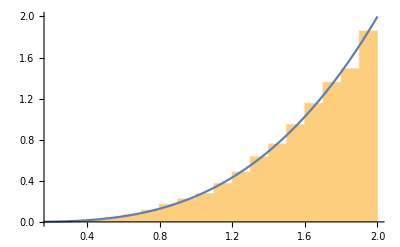

```mathematica
Show[Histogram[Table[xrand1[],10000],Automatic,"PDF"],Plot[xpdf1[x],{x,0,2}]]
```

```mathematica
yfunc1[y_]=y^5
ynorm1=Integrate[yfunc1[y],{y,0,5}]
ypdf1[y_]=yfunc1[y]/ynorm1
ycdf1[y_]=Integrate[ypdf1[yt],{yt,0,y}]
yicdf1[alpha_]=y/.Solve[ycdf1[y]==alpha,y][[2]]
yrand1[]:=yicdf1[RandomReal[]]
```

y^5

15625/6

(6 y^5)/15625

y^6/15625

5 alpha^(1/6)

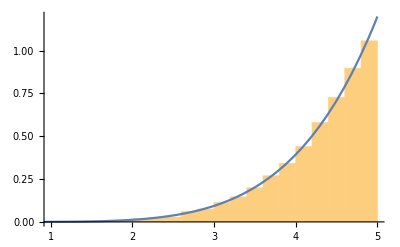

```mathematica
Show[Histogram[Table[yrand1[],10000],Automatic,"PDF"],Plot[ypdf1[y],{y,0,5}]]
```

```mathematica
zfunc1[z_]=Exp[-z]
znorm1=Integrate[zfunc1[z],{z,0,Infinity}]
zpdf1[z_]=zfunc1[z]/znorm1
zcdf1[z_]=Integrate[zpdf1[zt],{zt,0,z}]
zicdf1[alpha_]=z/.Solve[zcdf1[z]==alpha,z][[1]]/.C[1]->0
zrand1[]:=zicdf1[RandomReal[]]
```

ⅇ^-z

1

ⅇ^-z

1-Cosh[z]+Sinh[z]

Log[1/(1-alpha)]

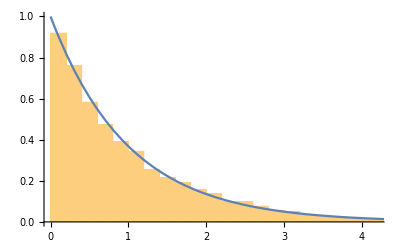

```mathematica
Show[Histogram[Table[zrand1[],10000],Automatic,"PDF"],Plot[zpdf1[z],{z,0,5}]]
```

```mathematica
NIntegrate[func1[x,y,z],{x,0,2},{y,0,5},{z,0,Infinity}]
```

36514.7

```mathematica
n=100000;
sum=0.0;
ifunc1[x_,y_,z_]=func1[x,y,z]/(xpdf1[x]*ypdf1[y]*zpdf1[z])
Do[sum+=ifunc1[x,y,z]/.{x->xrand1[],y->yrand1[],z->zrand1[]},{n}];
sum/n
```

31250/3 (3+Cos[x+y+z])

36510.9

Second function:

```mathematica
func2[x_,y_,z_]=x^3*y^5*Exp[-z*x*y]*(3+Cos[x+y+z])
```

ⅇ^(-x y z) x^3 y^5 (3+Cos[x+y+z])

```mathematica
xyznorm2=Integrate[x^3*y^5*Exp[-z*x*y],{x,0,2},{y,0,5},{z,0,Infinity}];
xyzdist2[x_,y_,z_]=x^3*y^5*Exp[-z*x*y]/xyznorm2
```

(3 ⅇ^(-x y z) x^3 y^5)/5000

```mathematica
xydist2[x_,y_]=Normal@Integrate[xyzdist2[x,y,z],{z,0,Infinity}]
```

(3 x^2 y^4)/5000

```mathematica
xdist2[x_]=Integrate[xydist2[x,y],{y,0,5}]
xcdf2[x_]=Integrate[xdist2[xt],{xt,0,x}]
xicdf2[v_]=x/.Solve[xcdf2[x]==v,x][[1]]
xrand2[]:=xicdf2[RandomReal[]]
```

(3 x^2)/8

x^3/8

2 v^(1/3)

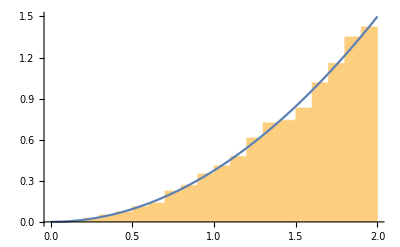

```mathematica
Show[Histogram[Table[xrand2[],10000],Automatic,"PDF"],Plot[xdist2[x],{x,0,2}]]
```

```mathematica
ynorm2[x_]=Integrate[xydist2[x,y],{y,0,5}]
ydist2[x_,y_]=xydist2[x,y]/ynorm2[x]
ycdf2[x_,y_]=Integrate[ydist2[x,yt],{yt,0,y}]
yicdf2[v_,x_]=y/.Solve[ycdf2[x,y]==v,y][[1]]
yrand2[x_]:=yicdf2[RandomReal[],x]
```

(3 x^2)/8

y^4/625

y^5/3125

5 v^(1/5)

```mathematica
Show[
Histogram3D[Table[{x,yrand2[x]}/.x->xrand2[],10000],Automatic,"PDF"],
Plot3D[xdist2[x]*ydist2[x,y],{x,0,2},{y,0,5},PlotRange->All,PlotStyle->Directive[Opacity[0.5],Red]]
]
```

-Graphics3D-

```mathematica
znorm2[x_,y_]=Normal@Integrate[xyzdist2[x,y,z],{z,0,Infinity}]
zdist2[x_,y_,z_]=xyzdist2[x,y,z]/znorm2[x,y]
zcdf2[x_,y_,z_]=Integrate[zdist2[x,y,zt],{zt,0,z}]
zicdf2[v_,x_,y_]=z/.Solve[zcdf2[x,y,z]==v,z][[1]]/.C[1]->0
zrand2[x_,y_]:=zicdf2[RandomReal[],x,y]
```

(3 x^2 y^4)/5000

ⅇ^(-x y z) x y

1-ⅇ^(-x y z)

Log[1/(1-v)]/(x y)

```mathematica
Show[
DensityPlot3D[xyzdist2[x,y,z],{x,0,2},{y,0,5},{z,0,1},
OpacityFunction->"Image3D", PlotLegends->Automatic],
ListPointPlot3D[Table[({x,y,zrand2[x,y]}/.y->yrand2[x])/.x->xrand2[],5000],
PlotStyle->Red]
]
```

-Graphics3D-

```mathematica
NIntegrate[func2[x,y,z],{x,0,2},{y,0,5},{z,0,Infinity}]
```

6174.82

```mathematica
n=100000;
Timing[
sum=0.0;
Do[
Module[
{xval,yval,zval},
xval=xrand2[];
yval=yrand2[xval];
zval=zrand2[xval,yval];
sum+=(3+Cos[x+y+z])/.{x->xval,y->yval,z->zval}
],
{n}
];
xyznorm2*sum/n
]
```

{2.10938,6172.98}